# Code for “Coexistence theory of mutualism” paper

## Figure 2

```mathematica
Clear["Global`*"]
```

### Scenario 1: Mutualisms influence plant coexistence even when commodities are not limiting

#### Scenario 1a: plants disproportionately reward the mutualistic partners upon which they rely

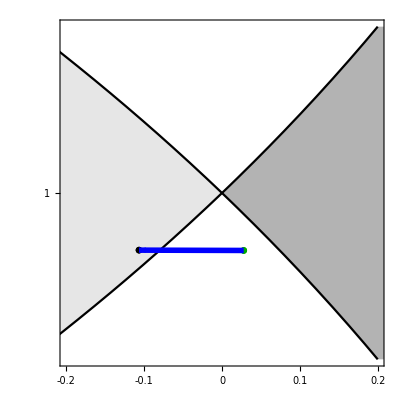

```mathematica
(* Parameters *)
param={b1->1,c11->1,c12->0.9,e11->0.1,e12->0.1,e13->0.1,v11->0.8,v12->0.2,v13->0,τ11->0,τ12->0,τ13->0,
b2->1,c21->1.05,c22->1,e21->0.1,e22->0.1,e23->0.1,v21->0.36,v22->0.63,v23->0.01,τ21->0,τ22->0,τ23->0,
β1->1,β2->1,bM3->1,δ1->1,δ2->1,δ3->1,μ11->3.2,μ21->1,μ12->1,μ22->5,μ13->0,μ23->1};

(* Intrinsic per capita growth rates and interaction coefficients *)
r1= b1+(e11 v11 β1)/δ1+(e12 v12 β2)/δ2+(e13 v13 bM3)/δ3;
r2= b2+(e21 v21 β1)/δ1+(e22 v22 β2)/δ2+(e23 v23 bM3)/δ3;
α12=1/r1(c12+e11 v11 v21 τ21+e12 v12 v22 τ22+e13 v13 v23 τ23-((e11 v11 v21 μ21)/δ1+(e12 v12 v22 μ22)/δ2+(e13 v13 v23 μ23)/δ3));
α21=1/r2(c21+e21 v21 v11 τ11+e22 v22 v12 τ12+e23 v23 v13 τ13-((e21 v21 v11 μ11)/δ1+(e22 v22 v12 μ12)/δ2+(e23 v23 v13 μ13)/δ3));
α11=1/r1( c11+e11 v11 v11 τ11+e12 v12 v12 τ12+e13 v13 v13 τ13-((e11 v11 v11 μ11)/δ1+(e12 v12 v12 μ12)/δ2+(e13 v13 v13 μ13)/δ3));
α22=1/r2(c22+e21 v21 v21 τ21+e22 v22 v22 τ22+e23 v23 v23 τ23-((e21 v21 v21 μ21)/δ1+(e22 v22 v22 μ22)/δ2+(e23 v23 v23 μ23)/δ3));

(* Niche and fitness difference *)
ρ=√((α12 α21)/(α11 α22));
κ2κ1=√((α12 α11)/(α21 α22));

(* Plots *)
(* Region plot showing interaction outcomes *)
RP1=Show[LogPlot[{1-x,1/(1-x)},{x,0,1},PlotRange->{{-0.2,0.2},{0.8,1.25}},Filling->1,FillingStyle->GrayLevel[0.7],PlotStyle->{{Black},{Black}}],LogPlot[{1-x,1/(1-x)},{x,-1,0},Filling->1,FillingStyle->GrayLevel[0.9],PlotStyle->{{Black},{Black}}],AxesOrigin->{-1,Log[0.4]},Frame->True,AspectRatio->1,FrameTicks->{{{{Log[0.8],0.8},{Log[1],1},{Log[1.25],1.25}},None},{{-0.2,-0.1,0,0.1,0.2},None}},FrameStyle->{{Black,Black},{Black,Black}},LabelStyle->Directive[FontSize->24]];
(* Points and arrows *)
pS1a=Show[
(* Resource competition *)
ListPlot[{{1-√((c12 c21)/(c11 c22)),Log[√((c12 c11)/(c21 c22))]}/.param},PlotMarkers->{Graphics[{EdgeForm[{Darker[Green],Thick}],FaceForm[Darker[Green]],Disk[]}],0.05}],
(* Competition and mutualism *)
ListPlot[{{1-ρ,Log[κ2κ1]}/.param},PlotMarkers->{Graphics[{EdgeForm[{Black}],FaceForm[Black],Disk[]}],0.05}],(* Arrow *)
ListLinePlot[{{1-√((c12 c21)/(c11 c22)),Log[√((c12 c11)/(c21 c22))]}/.param,{1-ρ,Log[κ2κ1]}/.param},PlotMarkers->None,PlotStyle->{Blue,Thickness[0.01]}]/.Line->Arrow];
Show[RP1,pS1a]
```

#### Scenario 1b: partner 2 acquires greater mutualistic benefits from both plant species than does partner 1

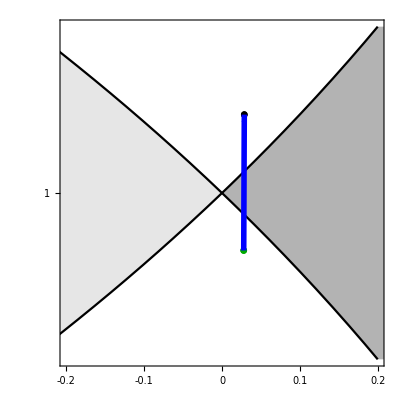

```mathematica
(* Parameters *)
param={b1->1,c11->1,c12->0.9,e11->0.1,e12->0.1,e13->0.1,v11->1.3,v12->0.7,v13->0,τ11->0,τ12->0,τ13->0,
b2->1,c21->1.05,c22->1,e21->0.1,e22->0.1,e23->0.1,v21->0.1,v22->1.9,v23->0.01,τ21->0,τ22->0,τ23->0,
β1->1,β2->1,bM3->1,δ1->1,δ2->1,δ3->1,μ11->0.04,μ21->0.1,μ12->2,μ22->0.7,μ13->0,μ23->1};

(* Intrinsic per capita growth rates and interaction coefficients *)
r1= b1+(e11 v11 β1)/δ1+(e12 v12 β2)/δ2+(e13 v13 bM3)/δ3;
r2= b2+(e21 v21 β1)/δ1+(e22 v22 β2)/δ2+(e23 v23 bM3)/δ3;
α12=1/r1(c12+e11 v11 v21 τ21+e12 v12 v22 τ22+e13 v13 v23 τ23-((e11 v11 v21 μ21)/δ1+(e12 v12 v22 μ22)/δ2+(e13 v13 v23 μ23)/δ3));
α21=1/r2(c21+e21 v21 v11 τ11+e22 v22 v12 τ12+e23 v23 v13 τ13-((e21 v21 v11 μ11)/δ1+(e22 v22 v12 μ12)/δ2+(e23 v23 v13 μ13)/δ3));
α11=1/r1( c11+e11 v11 v11 τ11+e12 v12 v12 τ12+e13 v13 v13 τ13-((e11 v11 v11 μ11)/δ1+(e12 v12 v12 μ12)/δ2+(e13 v13 v13 μ13)/δ3));
α22=1/r2(c22+e21 v21 v21 τ21+e22 v22 v22 τ22+e23 v23 v23 τ23-((e21 v21 v21 μ21)/δ1+(e22 v22 v22 μ22)/δ2+(e23 v23 v23 μ23)/δ3));

(* Niche and fitness difference *)
ρ=√((α12 α21)/(α11 α22));
κ2κ1=√((α12 α11)/(α21 α22));

(* Plots *)
(* Region plot showing interaction outcomes *)
RP1=Show[LogPlot[{1-x,1/(1-x)},{x,0,1},PlotRange->{{-0.2,0.2},{0.8,1.25}},Filling->1,FillingStyle->GrayLevel[0.7],PlotStyle->{{Black},{Black}}],LogPlot[{1-x,1/(1-x)},{x,-1,0},Filling->1,FillingStyle->GrayLevel[0.9],PlotStyle->{{Black},{Black}}],AxesOrigin->{-1,Log[0.4]},Frame->True,AspectRatio->1,FrameTicks->{{{{Log[0.8],0.8},{Log[1],1},{Log[1.25],1.25}},None},{{-0.2,-0.1,0,0.1,0.2},None}},FrameStyle->{{Black,Black},{Black,Black}},LabelStyle->Directive[FontSize->24]];
(* Points and arrows *)
pS1b=Show[
(* Resource competition *)
ListPlot[{{1-√((c12 c21)/(c11 c22)),Log[√((c12 c11)/(c21 c22))]}/.param},PlotMarkers->{Graphics[{EdgeForm[{Darker[Green],Thick}],FaceForm[Darker[Green]],Disk[]}],0.05}],
(* Competition and mutualism *)
ListPlot[{{1-ρ,Log[κ2κ1]}/.param},PlotMarkers->{Graphics[{EdgeForm[{Black}],FaceForm[Black],Disk[]}],0.05}],(* Arrow *)
ListLinePlot[{{1-√((c12 c21)/(c11 c22)),Log[√((c12 c11)/(c21 c22))]}/.param,{1-ρ,Log[κ2κ1]}/.param},PlotMarkers->None,PlotStyle->{Blue,Thickness[0.01]}]/.Line->Arrow];
Show[RP1,pS1b]
```

#### Figure 2a

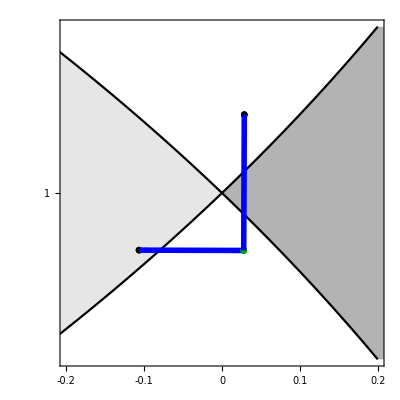

```mathematica
Show[RP1,pS1a,pS1b]
```

### Scenario 2: Mutualisms can promote coexistence even when they do not stabilize plant competition

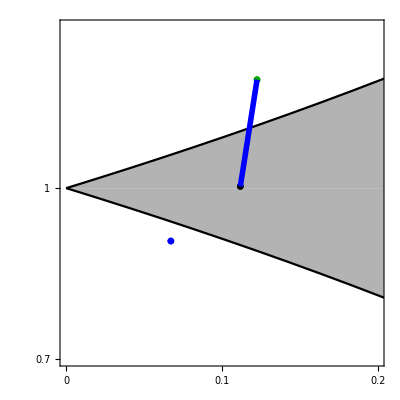

```mathematica
(* Parameters *)
param={b1->1,c11->1,c12->1.1,e11->0.5,e12->0.5,e13->0.5,v11->11,v12->9,v13->0,τ11->0.2,τ12->0.2,τ13->0.2,
b2->1,c21->0.7,c22->1,e21->0.1,e22->0.1,e23->0.1,v21->22.1,v22->25.5,v23->51,τ21->0.2,τ22->0.2,τ23->0.2,
β1->0.1,β2->0.1,bM3->0.1,δ1->1,δ2->1,δ3->1,μ11->0.25,μ21->0.1,μ12->0.1,μ22->0.3,μ13->0,μ23->0.19};

(* Intrinsic per capita growth rates and interaction coefficients *)
r1= b1+(e11 v11 β1)/δ1+(e12 v12 β2)/δ2+(e13 v13 bM3)/δ3;
r2= b2+(e21 v21 β1)/δ1+(e22 v22 β2)/δ2+(e23 v23 bM3)/δ3;
α12=1/r1(c12+e11 v11 v21 τ21+e12 v12 v22 τ22+e13 v13 v23 τ23-((e11 v11 v21 μ21)/δ1+(e12 v12 v22 μ22)/δ2+(e13 v13 v23 μ23)/δ3));
α21=1/r2(c21+e21 v21 v11 τ11+e22 v22 v12 τ12+e23 v23 v13 τ13-((e21 v21 v11 μ11)/δ1+(e22 v22 v12 μ12)/δ2+(e23 v23 v13 μ13)/δ3));
α11=1/r1( c11+e11 v11 v11 τ11+e12 v12 v12 τ12+e13 v13 v13 τ13-((e11 v11 v11 μ11)/δ1+(e12 v12 v12 μ12)/δ2+(e13 v13 v13 μ13)/δ3));
α22=1/r2(c22+e21 v21 v21 τ21+e22 v22 v22 τ22+e23 v23 v23 τ23-((e21 v21 v21 μ21)/δ1+(e22 v22 v22 μ22)/δ2+(e23 v23 v23 μ23)/δ3));

(* Niche and fitness difference *)
ρ=√((α12 α21)/(α11 α22));
1-ρ/.param;
κ2κ1=√((α12 α11)/(α21 α22));
κ2κ1/.param;

(* Plots *)
(* Region plot showing interaction outcomes *)
RP2=LogPlot[{1-x,1/(1-x)},{x,0,1},PlotRange->{{0,0.2},{0.7,1.4}},Filling->1,FillingStyle->GrayLevel[0.7],PlotStyle->{{Black},{Black}},Frame->True,AspectRatio->1,FrameTicks->{{{0.7,1,1.4},None},{{0,0.1,0.2},None}},FrameStyle->{{Black,Black},{Black,Black}},LabelStyle->Directive[FontSize->24]];
(* Points and arrows *)
pS2=Show[
(* Resource competition *)
ListPlot[{{1-√((c12 c21)/(c11 c22)),Log[√((c12 c11)/(c21 c22))]}/.param},PlotMarkers->{Graphics[{EdgeForm[{Darker[Green],Thick}],FaceForm[Darker[Green]],Disk[]}],0.05}],
(* Mutualism *)
ListPlot[{{1-ρ,Log[κ2κ1]}/.{b1->0,c11->1,c12->1,e11->0.5,e12->0.5,e13->0.5,v11->11,v12->9,v13->0,τ11->0.2,τ12->0.2,τ13->0,b2->0,c21->1,c22->1,e21->0.1,e22->0.1,e23->0.1,v21->22.1,v22->25.5,v23->51,τ21->0.2,τ22->0.2,τ23->0.2,β1->0.1,β2->0.1,bM3->0.1,δ1->1,δ2->1,δ3->1,μ11->0.25,μ21->0.1,μ12->0.1,μ22->0.3,μ13->0,μ23->0.19}},PlotMarkers->{Graphics[{EdgeForm[{Blue}],FaceForm[Blue],Disk[]}],0.05}],
(* Competition and mutualism *)
ListPlot[{{1-ρ,Log[κ2κ1]}/.param},PlotMarkers->{Graphics[{EdgeForm[{Black}],FaceForm[Black],Disk[]}],0.05}],(* Arrows *)
ListLinePlot[{{1-√((c12 c21)/(c11 c22)),Log[√((c12 c11)/(c21 c22))]}/.param,{1-ρ,Log[κ2κ1]}/.param},PlotMarkers->None,PlotStyle->{Blue,Thickness[0.01]}]/.Line->Arrow];
Show[RP2,pS2]
```

### Scenario 3: Mutualisms drive competitive exclusion when plants would otherwise coexist

0.035278

0.525489

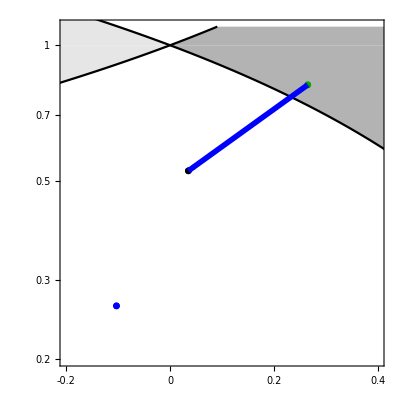

```mathematica
(* Parameters *)
param={b1->1,c11->1,c12->0.6,e11->0.1,e12->0.1,e13->0.1,v11->32,v12->68,v13->0,τ11->0.12,τ12->0.12,τ13->0.12,
b2->1,c21->0.9,c22->1,e21->0.1,e22->0.1,e23->0.1,v21->3,v22->17,v23->9.5,τ21->0.2,τ22->0.2,τ23->0.2,
β1->0.1,β2->0.1,bM3->0.1,δ1->1,δ2->1,δ3->1,μ11->0.2,μ21->0.1,μ12->0.1,μ22->0.2,μ13->0,μ23->0.1};

(* Intrinsic per capita growth rates and interaction coefficients *)
r1= b1+(e11 v11 β1)/δ1+(e12 v12 β2)/δ2+(e13 v13 bM3)/δ3;
r2= b2+(e21 v21 β1)/δ1+(e22 v22 β2)/δ2+(e23 v23 bM3)/δ3;
α12=1/r1(c12+e11 v11 v21 τ21+e12 v12 v22 τ22+e13 v13 v23 τ23-((e11 v11 v21 μ21)/δ1+(e12 v12 v22 μ22)/δ2+(e13 v13 v23 μ23)/δ3));
α21=1/r2(c21+e21 v21 v11 τ11+e22 v22 v12 τ12+e23 v23 v13 τ13-((e21 v21 v11 μ11)/δ1+(e22 v22 v12 μ12)/δ2+(e23 v23 v13 μ13)/δ3));
α11=1/r1( c11+e11 v11 v11 τ11+e12 v12 v12 τ12+e13 v13 v13 τ13-((e11 v11 v11 μ11)/δ1+(e12 v12 v12 μ12)/δ2+(e13 v13 v13 μ13)/δ3));
α22=1/r2(c22+e21 v21 v21 τ21+e22 v22 v22 τ22+e23 v23 v23 τ23-((e21 v21 v21 μ21)/δ1+(e22 v22 v22 μ22)/δ2+(e23 v23 v23 μ23)/δ3));

(* Niche and fitness difference *)
ρ=√((α12 α21)/(α11 α22));
1-ρ/.param
κ2κ1=√((α12 α11)/(α21 α22));
κ2κ1/.param

(* Plots *)
(* Region plot showing interaction outcomes *)
RP3=Show[LogPlot[{1-x,1/(1-x)},{x,0,1},PlotRange->{{-0.2,0.4},{0.2,1.1}},Filling->1,FillingStyle->GrayLevel[0.7],PlotStyle->{{Black},{Black}}],LogPlot[{1-x,1/(1-x)},{x,-1,0},Filling->1,FillingStyle->GrayLevel[0.9],PlotStyle->{{Black},{Black}}],AxesOrigin->{-1,Log[0.2]},Frame->True,AspectRatio->1,FrameTicks->{{{{Log[0.2],0.2},{Log[0.5],0.5},{Log[1],1}},None},{{-0.2,0,0.2,0.4},None}},FrameStyle->{{Black,Black},{Black,Black}},LabelStyle->Directive[FontSize->24]];
(* Points and arrows *)
pS3=Show[
(* Resource competition *)
ListPlot[{{1-√((c12 c21)/(c11 c22)),Log[√((c12 c11)/(c21 c22))]}/.param},PlotMarkers->{Graphics[{EdgeForm[{Darker[Green],Thick}],FaceForm[Darker[Green]],Disk[]}],0.05}],
(* Mutualism *)
ListPlot[{{1-ρ,Log[κ2κ1]}/.{b1->0,c11->1,c12->1,e11->0.1,e12->0.1,e13->0.1,v11->32,v12->68,v13->0,τ11->0.12,τ12->0.12,τ13->0.12,b2->0,c21->1,c22->1,e21->0.1,e22->0.1,e23->0.1,v21->3,v22->17,v23->9.5,τ21->0.2,τ22->0.2,τ23->0.2,β1->0.1,β2->0.1,bM3->0.1,δ1->1,δ2->1,δ3->1,μ11->0.2,μ21->0.1,μ12->0.1,μ22->0.2,μ13->0,μ23->0.1}},PlotMarkers->{Graphics[{EdgeForm[{Blue}],FaceForm[Blue],Disk[]}],0.05}],
(* Competition and mutualism *)
ListPlot[{{1-ρ,Log[κ2κ1]}/.param},PlotMarkers->{Graphics[{EdgeForm[{Black}],FaceForm[Black],Disk[]}],0.05}],(* Arrows *)
ListLinePlot[{{1-√((c12 c21)/(c11 c22)),Log[√((c12 c11)/(c21 c22))]}/.param,{1-ρ,Log[κ2κ1]}/.param},PlotMarkers->None,PlotStyle->{Blue,Thickness[0.01]}]/.Line->Arrow];
Show[RP3,pS3]
```

### Scenario 4: Systematic changes in the parameters underlying the niche and fitness differences

#### Scenario 4a (Figure 2d): Changes in v

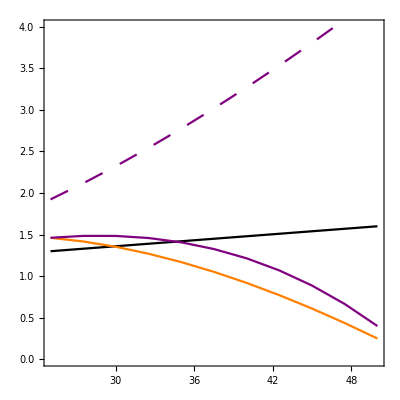

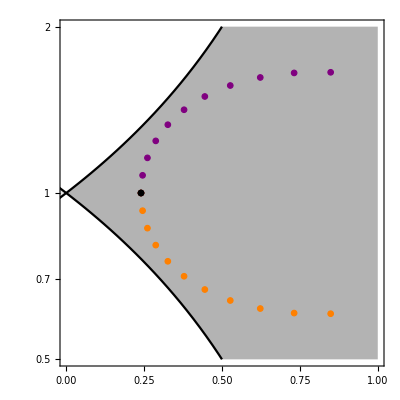

```mathematica
(* Parameters *)
param={b1->1,c11->1,c12->0.4,e11->0.1,e12->0.1,e13->0.1,v13->0,τ11->0.2,τ12->0.2,τ13->0.2,
b2->1,c21->0.4,c22->1,e21->0.1,e22->0.1,e23->0.1,v23->0,τ21->0.2,τ22->0.2,τ23->0.2,
β1->0.1,β2->0.1,bM3->0.1,δ1->1,δ2->1,δ3->1,μ11->0.18,μ21->0.1,μ12->0.1,μ22->0.18,μ13->0,μ23->0};
steps=10;

(* Intrinsic per capita growth rates and interaction coefficients *)
r1= b1+(e11 v11 β1)/δ1+(e12 v12 β2)/δ2+(e13 v13 bM3)/δ3;
r2= b2+(e21 v21 β1)/δ1+(e22 v22 β2)/δ2+(e23 v23 bM3)/δ3;
α12=1/r1(c12+e11 v11 v21 τ21+e12 v12 v22 τ22+e13 v13 v23 τ23-((e11 v11 v21 μ21)/δ1+(e12 v12 v22 μ22)/δ2+(e13 v13 v23 μ23)/δ3));
α21=1/r2(c21+e21 v21 v11 τ11+e22 v22 v12 τ12+e23 v23 v13 τ13-((e21 v21 v11 μ11)/δ1+(e22 v22 v12 μ12)/δ2+(e23 v23 v13 μ13)/δ3));
α11=1/r1( c11+e11 v11 v11 τ11+e12 v12 v12 τ12+e13 v13 v13 τ13-((e11 v11 v11 μ11)/δ1+(e12 v12 v12 μ12)/δ2+(e13 v13 v13 μ13)/δ3));
α22=1/r2(c22+e21 v21 v21 τ21+e22 v22 v22 τ22+e23 v23 v23 τ23-((e21 v21 v21 μ21)/δ1+(e22 v22 v22 μ22)/δ2+(e23 v23 v23 μ23)/δ3));

(* Niche and fitness difference *)
ρ=√((α12 α21)/(α11 α22));
κ2κ1=√((α12 α11)/(α21 α22));

(* Define matrices with niche and fitness differences as model parameter is varied *)
v1Matrix=v2Matrix={{1-ρ/.param/.v11->25/.v12->5/.v21->5/.v22->25,
Log[κ2κ1]/.param/.v11->25/.v12->5/.v21->5/.v22->25}}; 

(* Define matrices with parameter being systematically varied and resulting r and α terms for Appendix S5 *)
v1r={{v11/.v11->25,r1/.param/.v11->25/.v12->5/.v21->5/.v22->25}};
v1α12={{v11/.v11->25,α12/.param/.v11->25/.v12->5/.v21->5/.v22->25}};
v1α11={{v11/.v11->25,α11/.param/.v11->25/.v12->5/.v21->5/.v22->25}};
v1α21={{v11/.v11->25,α21/.param/.v11->25/.v12->5/.v21->5/.v22->25}};

(* Systematically vary model parameter by stepsize 0.1 t and update matrices of niche and fitness differences as well as matrices of r and α terms *)
For[t=1,t≤steps,t++,
(* Increase v1 *)
v1Matrix=AppendTo[v1Matrix,{1-ρ/.param/.v11->25(1+0.1t)/.v12->5(1+0.1t)/.v21->5(1-0.1t)/.v22->25(1-0.1t),Log[κ2κ1]/.param/.v11->25(1+0.1t)/.v12->5(1+0.1t)/.v21->5(1-0.1t)/.v22->25(1-0.1t)}];
v1r=AppendTo[v1r,{v11/.v11->25(1+0.1t),r1/.param/.v11->25(1+0.1t)/.v12->5(1+0.1t)/.v21->5(1-0.1t)/.v22->25(1-0.1t)}];v1α12=AppendTo[v1α12,{v11/.v11->25(1+0.1t),α12/.param/.v11->25(1+0.1t)/.v12->5(1+0.1t)/.v21->5(1-0.1t)/.v22->25(1-0.1t)}];
v1α11=AppendTo[v1α11,{v11/.v11->25(1+0.1t),α11/.param/.v11->25(1+0.1t)/.v12->5(1+0.1t)/.v21->5(1-0.1t)/.v22->25(1-0.1t)}];
v1α21=AppendTo[v1α21,{v11/.v11->25(1+0.1t),α21/.param/.v11->25(1+0.1t)/.v12->5(1+0.1t)/.v21->5(1-0.1t)/.v22->25(1-0.1t)}];
(* Increase v2 *)
v2Matrix=AppendTo[v2Matrix,{1-ρ/.param/.v11->25(1-0.1t)/.v12->5(1-0.1t)/.v21->5(1+0.1t)/.v22->25(1+0.1t),Log[κ2κ1]/.param/.v11->25(1-0.1t)/.v12->5(1-0.1t)/.v21->5(1+0.1t)/.v22->25(1+0.1t)}]]

(* See arrays if needed *)
v1Matrix//MatrixForm;

(* Plot r and alphas for Appendix S5: Figure 1a *)
ListLinePlot[{v1r,v1α12,v1α11,v1α21},PlotStyle->{Black,Orange,{Purple,Dashing[Large]},Purple},Frame->True,FrameStyle->{{Black,Black},{Black,Black}},PlotRange->{{25,50},{0,4}},AxesOrigin->{25,0},AspectRatio->1,LabelStyle->Directive[FontSize->24]]

(* Plots *)
(* Region plot showing interaction outcomes *)
RP4a=Show[LogPlot[{1-x,1/(1-x)},{x,0,1},PlotRange->{{0,1},{0.5,2}},Filling->1,FillingStyle->GrayLevel[0.7],PlotStyle->{{Black},{Black}}],LogPlot[{1-x,1/(1-x)},{x,-1,0},Filling->1,FillingStyle->GrayLevel[0.9],PlotStyle->{{Black},{Black}}],AxesOrigin->{-1,Log[0.4]},Frame->True,AspectRatio->1,FrameTicks->{{{{Log[0.5],0.5},{Log[1],1},{Log[2],2}},None},{Automatic,None}},FrameStyle->{{Black,Black},{Black,Black}},LabelStyle->Directive[FontSize->24]];
(* Competition and mutualism *)
pS4a=ListPlot[{{1-ρ,Log[κ2κ1]}/.param/.v11->25/.v12->5/.v21->5/.v22->25},PlotMarkers->{Graphics[{EdgeForm[{Black,Thick}],FaceForm[Black],Disk[]}],0.051}];
(* Increase in v_1k *)
S4v1=ListPlot[{v1Matrix},PlotMarkers->{Graphics[{EdgeForm[{Purple,Thick}],FaceForm[Purple],Disk[]}],0.02}];  
(* Increase in v_2k *)
S4v2=ListPlot[{v2Matrix},PlotMarkers->{Graphics[{EdgeForm[{Orange,Thick}],FaceForm[Orange],Disk[]}],0.02}];  (* Combine plots: orange and purple dots overlain with arrows in Adobe Illustrator to generate panel 2d *)
p4a=Show[RP4a,S4v1,S4v2,pS4a]
```

#### Scenario 4b (Figure 2e): Changes in e

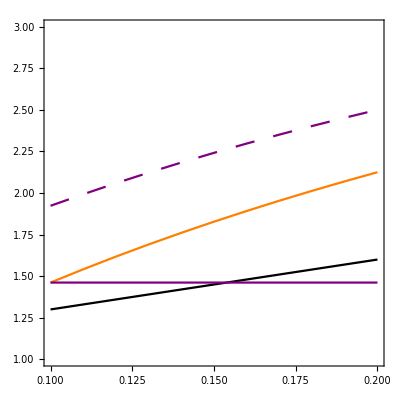

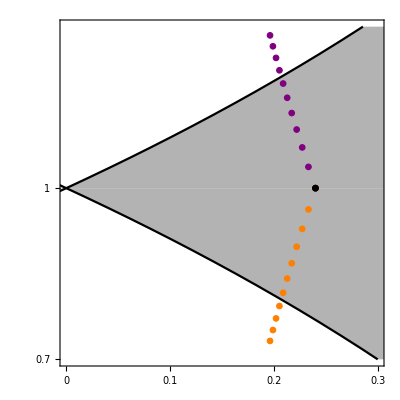

```mathematica
(* Parameters *)
param={b1->1,c11->1,c12->0.4,v11->25,v12->5,v13->0,τ11->0.2,τ12->0.2,τ13->0.2,b2->1,c21->0.4,c22->1,v21->5,v22->25,v23->0,τ21->0.2,τ22->0.2,τ23->0.2,β1->0.1,β2->0.1,bM3->0.1,δ1->1,δ2->1,δ3->1,μ11->0.18,μ21->0.1,μ12->0.1,μ22->0.18,μ13->0,μ23->0};
steps=10;

(* Intrinsic per capita growth rates and interaction coefficients *)
r1= b1+(e11 v11 β1)/δ1+(e12 v12 β2)/δ2+(e13 v13 bM3)/δ3;
r2= b2+(e21 v21 β1)/δ1+(e22 v22 β2)/δ2+(e23 v23 bM3)/δ3;
α12=1/r1(c12+e11 v11 v21 τ21+e12 v12 v22 τ22+e13 v13 v23 τ23-((e11 v11 v21 μ21)/δ1+(e12 v12 v22 μ22)/δ2+(e13 v13 v23 μ23)/δ3));
α21=1/r2(c21+e21 v21 v11 τ11+e22 v22 v12 τ12+e23 v23 v13 τ13-((e21 v21 v11 μ11)/δ1+(e22 v22 v12 μ12)/δ2+(e23 v23 v13 μ13)/δ3));
α11=1/r1( c11+e11 v11 v11 τ11+e12 v12 v12 τ12+e13 v13 v13 τ13-((e11 v11 v11 μ11)/δ1+(e12 v12 v12 μ12)/δ2+(e13 v13 v13 μ13)/δ3));
α22=1/r2(c22+e21 v21 v21 τ21+e22 v22 v22 τ22+e23 v23 v23 τ23-((e21 v21 v21 μ21)/δ1+(e22 v22 v22 μ22)/δ2+(e23 v23 v23 μ23)/δ3));

(* Niche and fitness difference *)
ρ=√((α12 α21)/(α11 α22));
κ2κ1=√((α12 α11)/(α21 α22));

(* Define matrices with niche and fitness differences as model parameter is varied *)
e1Matrix=e2Matrix={{1-ρ/.param/.e11->0.1/.e21->0.1/.e12->0.1/.e22->0.1,
Log[κ2κ1]/.param/.e11->0.1/.e21->0.1/.e12->0.1/.e22->0.1}}; 

(* Define matrices with parameter being systematically varied and resulting r and α terms for Appendix S5 *)
e1r={{e11/.e11->0.1,r1/.param/.e11->0.1/.e21->0.1/.e12->0.1/.e22->0.1}};
e1α12={{e11/.e11->0.1,α12/.param/.e11->0.1/.e21->0.1/.e12->0.1/.e22->0.1}};
e1α11={{e11/.e11->0.1,α11/.param/.e11->0.1/.e21->0.1/.e12->0.1/.e22->0.1}};
e1α21={{e11/.e11->0.1,α21/.param/.e11->0.1/.e21->0.1/.e12->0.1/.e22->0.1}};

(* Systematically vary model parameter by stepsize 0.1 t and update matrices of niche and fitness differences as well as matrices of r and α terms *)
For[t=1,t≤steps,t++,
(* Increase e1k *)
e1Matrix=AppendTo[e1Matrix,{1-ρ/.param/.e11->0.1(1+0.1t)/.e21->0.1/.e12->0.1(1+0.1t)/.e22->0.1,Log[κ2κ1]/.param/.e11->0.1(1+0.1t)/.e21->0.1/.e12->0.1(1+0.1t)/.e22->0.1}];
e1r=AppendTo[e1r,{e11/.e11->0.1(1+0.1t),r1/.param/.e11->0.1(1+0.1t)/.e21->0.1/.e12->0.1(1+0.1t)/.e22->0.1}];e1α12=AppendTo[e1α12,{e11/.e11->0.1(1+0.1t),α12/.param/.e11->0.1(1+0.1t)/.e21->0.1/.e12->0.1(1+0.1t)/.e22->0.1}];
e1α11=AppendTo[e1α11,{e11/.e11->0.1(1+0.1t),α11/.param/.e11->0.1(1+0.1t)/.e21->0.1/.e12->0.1(1+0.1t)/.e22->0.1}];
e1α21=AppendTo[e1α21,{e11/.e11->0.1(1+0.1t),α21/.param/.e11->0.1(1+0.1t)/.e21->0.1/.e12->0.1(1+0.1t)/.e22->0.1}];
(* Increase e2k *)
e2Matrix=AppendTo[e2Matrix,{1-ρ/.param/.e11->0.1/.e21->0.1(1+0.1t)/.e12->0.1/.e22->0.1(1+0.1t),Log[κ2κ1]/.param/.e11->0.1/.e21->0.1(1+0.1t)/.e12->0.1/.e22->0.1(1+0.1t)}]]

(* See arrays if needed *)
e1Matrix//MatrixForm;

(* Plot r and alphas for Appendix S5: Figure 1b *)
ListLinePlot[{e1r,e1α12,e1α11,e1α21},PlotStyle->{Black,Orange,{Purple,Dashing[Large]},Purple},Frame->True,FrameStyle->{{Black,Black},{Black,Black}},PlotRange->{{0.1,0.2},{1,3}},AxesOrigin->{0.1,1},AspectRatio->1,LabelStyle->Directive[FontSize->24]]

(* Plots *)
(* Region plot showing interaction outcomes *)
RP4b=Show[LogPlot[{1-x,1/(1-x)},{x,0,1},PlotRange->{{0,0.3},{0.7,1.4}},Filling->1,FillingStyle->GrayLevel[0.7],PlotStyle->{{Black},{Black}}],LogPlot[{1-x,1/(1-x)},{x,-1,0},Filling->1,FillingStyle->GrayLevel[0.9],PlotStyle->{{Black},{Black}}],AxesOrigin->{-1,Log[0.4]},Frame->True,AspectRatio->1,FrameTicks->{{{{Log[0.7],0.7},{Log[1],1},{Log[1.4],1.4}},None},{{0,0.1,0.2,0.3},None}},FrameStyle->{{Black,Black},{Black,Black}},LabelStyle->Directive[FontSize->24]];
(* Competition and mutualism *)
pS4b=ListPlot[{{1-ρ,Log[κ2κ1]}/.param/.e11->0.1/.e21->0.1/.e12->0.1/.e22->0.1},PlotMarkers->{Graphics[{EdgeForm[{Black,Thick}],FaceForm[Black],Disk[]}],0.051}];
(* Increase in e_1k *)
S4e1=ListPlot[{e1Matrix},PlotMarkers->{Graphics[{EdgeForm[{Purple,Thick}],FaceForm[Purple],Disk[]}],0.02}];  
(* Increase in e_2k *)
S4e2=ListPlot[{e2Matrix},PlotMarkers->{Graphics[{EdgeForm[{Orange,Thick}],FaceForm[Orange],Disk[]}],0.02}];  (* Combine plots: orange and purple dots overlain with arrows in Adobe Illustrator to generate panel 2d *)
p4b=Show[RP4b,S4e1,S4e2,pS4b]
```

#### Scenario 4c (Figure 2f): Changes in μ

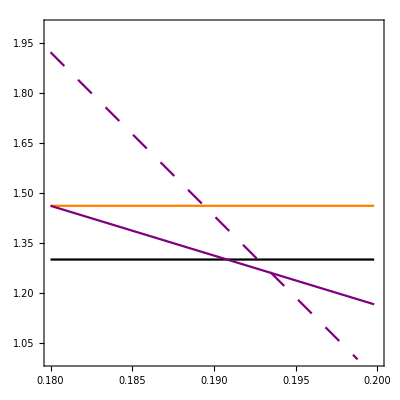

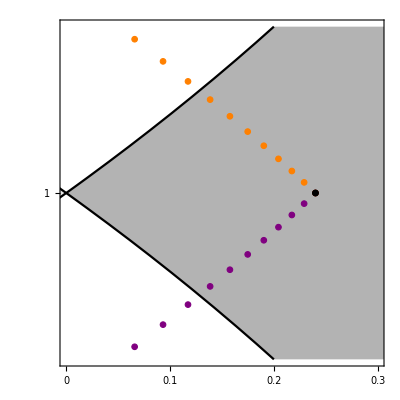

```mathematica
(* Parameters *)
param={b1->1,c11->1,c12->0.4,e11->0.1,e12->0.1,e13->0.1,v11->25,v12->5,v13->0,τ11->0.2,τ12->0.2,τ13->0.2,
b2->1,c21->0.4,c22->1,e21->0.1,e22->0.1,e23->0.1,v21->5,v22->25,v23->0,τ21->0.2,τ22->0.2,τ23->0.2,
β1->0.1,β2->0.1,bM3->0.1,δ1->1,δ2->1,δ3->1,μ13->0,μ23->0};
steps=11;

(* Intrinsic per capita growth rates and interaction coefficients *)
r1= b1+(e11 v11 β1)/δ1+(e12 v12 β2)/δ2+(e13 v13 bM3)/δ3;
r2= b2+(e21 v21 β1)/δ1+(e22 v22 β2)/δ2+(e23 v23 bM3)/δ3;
α12=1/r1(c12+e11 v11 v21 τ21+e12 v12 v22 τ22+e13 v13 v23 τ23-((e11 v11 v21 μ21)/δ1+(e12 v12 v22 μ22)/δ2+(e13 v13 v23 μ23)/δ3));
α21=1/r2(c21+e21 v21 v11 τ11+e22 v22 v12 τ12+e23 v23 v13 τ13-((e21 v21 v11 μ11)/δ1+(e22 v22 v12 μ12)/δ2+(e23 v23 v13 μ13)/δ3));
α11=1/r1( c11+e11 v11 v11 τ11+e12 v12 v12 τ12+e13 v13 v13 τ13-((e11 v11 v11 μ11)/δ1+(e12 v12 v12 μ12)/δ2+(e13 v13 v13 μ13)/δ3));
α22=1/r2(c22+e21 v21 v21 τ21+e22 v22 v22 τ22+e23 v23 v23 τ23-((e21 v21 v21 μ21)/δ1+(e22 v22 v22 μ22)/δ2+(e23 v23 v23 μ23)/δ3));

(* Niche and fitness difference *)
ρ=√((α12 α21)/(α11 α22));
κ2κ1=√((α12 α11)/(α21 α22));

(* Define matrices with niche and fitness differences as model parameter is varied *)
μ1Matrix=μ2Matrix={{1-ρ/.param/.μ11->0.18/.μ21->0.1/.μ12->0.1/.μ22->0.18,
Log[κ2κ1]/.param/.μ11->0.18/.μ21->0.1/.μ12->0.1/.μ22->0.18}}; 

(* Define matrices with parameter being systematically varied and resulting r and α terms for Appendix S5 *)
μ1r={{μ11/.μ11->0.18,r1/.param/.μ11->0.18/.μ21->0.1/.μ12->0.1/.μ22->0.18}};
μ1α12={{μ11/.μ11->0.18,α12/.param/.μ11->0.18/.μ21->0.1/.μ12->0.1/.μ22->0.18}};
μ1α11={{μ11/.μ11->0.18,α11/.param/.μ11->0.18/.μ21->0.1/.μ12->0.1/.μ22->0.18}};
μ1α21={{μ11/.μ11->0.18,α21/.param/.μ11->0.18/.μ21->0.1/.μ12->0.1/.μ22->0.18}};

(* Systematically vary model parameter by stepsize 0.1 t and update matrices of niche and fitness differences as well as matrices of r and α terms *)
For[t=1,t≤steps,t++,
(* Increase μ1k *)
μ1Matrix=AppendTo[μ1Matrix,{1-ρ/.param/.μ11->0.18(1+0.01t)/.μ21->0.1/.μ12->0.1(1+0.01t)/.μ22->0.18,Log[κ2κ1]/.param/.μ11->0.18(1+0.01t)/.μ21->0.1/.μ12->0.1(1+0.01t)/.μ22->0.18}];
μ1r=AppendTo[μ1r,{μ11/.μ11->0.18(1+0.01t),r1/.param/.μ11->0.18(1+0.01t)/.μ21->0.1/.μ12->0.1(1+0.01t)/.μ22->0.18}];μ1α12=AppendTo[μ1α12,{μ11/.μ11->0.18(1+0.01t),α12/.param/.μ11->0.18(1+0.01t)/.μ21->0.1/.μ12->0.1(1+0.01t)/.μ22->0.18}];
μ1α11=AppendTo[μ1α11,{μ11/.μ11->0.18(1+0.01t),α11/.param/.μ11->0.18(1+0.01t)/.μ21->0.1/.μ12->0.1(1+0.01t)/.μ22->0.18}];
μ1α21=AppendTo[μ1α21,{μ11/.μ11->0.18(1+0.01t),α21/.param/.μ11->0.18(1+0.01t)/.μ21->0.1/.μ12->0.1(1+0.01t)/.μ22->0.18}];
(* Increase μ2k *)
μ2Matrix=AppendTo[μ2Matrix,{1-ρ/.param/.μ11->0.18/.μ21->0.1(1+0.01t)/.μ12->0.1/.μ22->0.18(1+0.01t),Log[κ2κ1]/.param/.μ11->0.18/.μ21->0.1(1+0.01t)/.μ12->0.1/.μ22->0.18(1+0.01t)}]]

(* See arrays if needed *)
μ1Matrix//MatrixForm;

(* Plot r and alphas for Appendix S5: Figure 1c *)
ListLinePlot[{μ1r,μ1α12,μ1α11,μ1α21},PlotStyle->{Black,Orange,{Purple,Dashing[Large]},Purple},Frame->True,FrameStyle->{{Black,Black},{Black,Black}},PlotRange->{{0.18,0.2},{1,2}},AxesOrigin->{0.18,1},AspectRatio->1,LabelStyle->Directive[FontSize->24]]

(* Plots *)
(* Region plot showing interaction outcomes *)
RP4c=Show[LogPlot[{1-x,1/(1-x)},{x,0,1},PlotRange->{{0,0.3},{0.8,1.25}},Filling->1,FillingStyle->GrayLevel[0.7],PlotStyle->{{Black},{Black}}],LogPlot[{1-x,1/(1-x)},{x,-1,0},Filling->1,FillingStyle->GrayLevel[0.9],PlotStyle->{{Black},{Black}}],AxesOrigin->{-1,Log[0.4]},Frame->True,AspectRatio->1,FrameTicks->{{{{Log[0.8],0.8},{Log[1],1},{Log[1.25],1.25}},None},{{0,0.1,0.2,0.3},None}},FrameStyle->{{Black,Black},{Black,Black}},LabelStyle->Directive[FontSize->24]];
(* Competition and mutualism *)
pS4c=ListPlot[{{1-ρ,Log[κ2κ1]}/.param/.μ11->0.18/.μ21->0.1/.μ12->0.1/.μ22->0.18},PlotMarkers->{Graphics[{EdgeForm[{Black,Thick}],FaceForm[Black],Disk[]}],0.051}];
(* Increase in μ_1k *)
S4μ1=ListPlot[{μ1Matrix},PlotMarkers->{Graphics[{EdgeForm[{Purple,Thick}],FaceForm[Purple],Disk[]}],0.02}];  
(* Increase in μ_2k *)
S4μ2=ListPlot[{μ2Matrix},PlotMarkers->{Graphics[{EdgeForm[{Orange,Thick}],FaceForm[Orange],Disk[]}],0.02}];  (* Combine plots: orange and purple dots overlain with arrows in Adobe Illustrator to generate panel 2d *)
p4c=Show[RP4c,S4μ1,S4μ2,pS4c]
```

#### Scenario 4d (Figure 2g): Changes in τ

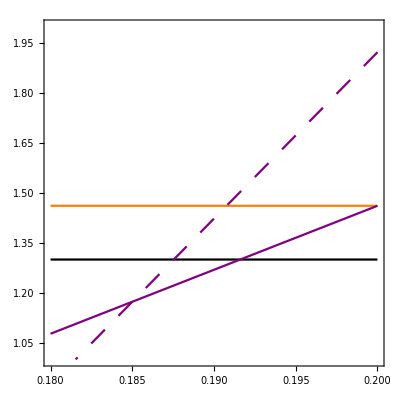

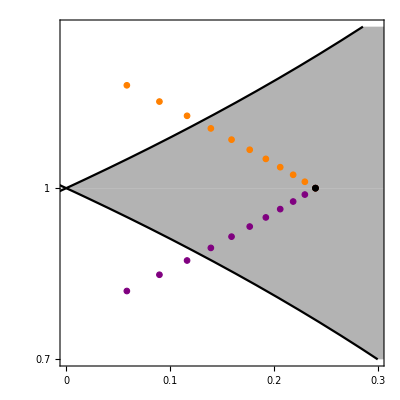

```mathematica
(* Parameters *)
param={b1->1,c11->1,c12->0.4,e11->0.1,e12->0.1,e13->0.1,v11->25,v12->5,v13->0,
b2->1,c21->0.4,c22->1,e21->0.1,e22->0.1,e23->0.1,v21->5,v22->25,v23->0,
β1->0.1,β2->0.1,bM3->0.1,δ1->1,δ2->1,δ3->1,μ11->0.18,μ21->0.1,μ12->0.1,μ22->0.18,μ13->0,μ23->0};
steps=10;

(* Intrinsic per capita growth rates and interaction coefficients *)
r1= b1+(e11 v11 β1)/δ1+(e12 v12 β2)/δ2+(e13 v13 bM3)/δ3;
r2= b2+(e21 v21 β1)/δ1+(e22 v22 β2)/δ2+(e23 v23 bM3)/δ3;
α12=1/r1(c12+e11 v11 v21 τ21+e12 v12 v22 τ22+e13 v13 v23 τ23-((e11 v11 v21 μ21)/δ1+(e12 v12 v22 μ22)/δ2+(e13 v13 v23 μ23)/δ3));
α21=1/r2(c21+e21 v21 v11 τ11+e22 v22 v12 τ12+e23 v23 v13 τ13-((e21 v21 v11 μ11)/δ1+(e22 v22 v12 μ12)/δ2+(e23 v23 v13 μ13)/δ3));
α11=1/r1( c11+e11 v11 v11 τ11+e12 v12 v12 τ12+e13 v13 v13 τ13-((e11 v11 v11 μ11)/δ1+(e12 v12 v12 μ12)/δ2+(e13 v13 v13 μ13)/δ3));
α22=1/r2(c22+e21 v21 v21 τ21+e22 v22 v22 τ22+e23 v23 v23 τ23-((e21 v21 v21 μ21)/δ1+(e22 v22 v22 μ22)/δ2+(e23 v23 v23 μ23)/δ3));

(* Niche and fitness difference *)
ρ=√((α12 α21)/(α11 α22));
κ2κ1=√((α12 α11)/(α21 α22));

(* Define matrices with niche and fitness differences as model parameter is varied *)
τ1Matrix=τ2Matrix={{1-ρ/.param/.τ11->0.2/.τ21->0.2/.τ12->0.2/.τ22->0.2,
Log[κ2κ1]/.param/.τ11->0.2/.τ21->0.2/.τ12->0.2/.τ22->0.2}}; 

(* Define matrices with parameter being systematically varied and resulting r and α terms for Appendix S5 *)
τ1r={{τ11/.τ11->0.2,r1/.param/.τ11->0.2/.τ21->0.2/.τ12->0.2/.τ22->0.2}};
τ1α12={{τ11/.τ11->0.2,α12/.param/.τ11->0.2/.τ21->0.2/.τ12->0.2/.τ22->0.2}};
τ1α11={{τ11/.τ11->0.2,α11/.param/.τ11->0.2/.τ21->0.2/.τ12->0.2/.τ22->0.2}};
τ1α21={{τ11/.τ11->0.2,α21/.param/.τ11->0.2/.τ21->0.2/.τ12->0.2/.τ22->0.2}};

(* Systematically vary model parameter by stepsize 0.01 t and update matrices of niche and fitness differences as well as matrices of r and α terms *)
For[t=1,t≤steps,t++,
(* Increase τ1k *)
τ1Matrix=AppendTo[τ1Matrix,{1-ρ/.param/.τ11->0.2(1-0.01t)/.τ21->0.2/.τ12->0.2(1-0.01t)/.τ22->0.2,Log[κ2κ1]/.param/.τ11->0.2(1-0.01t)/.τ21->0.2/.τ12->0.2(1-0.01t)/.τ22->0.2}];
τ1r=AppendTo[τ1r,{τ11/.τ11->0.2(1-0.01t),r1/.param/.τ11->0.2(1-0.01t)/.τ21->0.2/.τ12->0.2(1-0.01t)/.τ22->0.2}];τ1α12=AppendTo[τ1α12,{τ11/.τ11->0.2(1-0.01t),α12/.param/.τ11->0.2(1-0.01t)/.τ21->0.2/.τ12->0.2(1-0.01t)/.τ22->0.2}];
τ1α11=AppendTo[τ1α11,{τ11/.τ11->0.2(1-0.01t),α11/.param/.τ11->0.2(1-0.01t)/.τ21->0.2/.τ12->0.2(1-0.01t)/.τ22->0.2}];
τ1α21=AppendTo[τ1α21,{τ11/.τ11->0.2(1-0.01t),α21/.param/.τ11->0.2(1-0.01t)/.τ21->0.2/.τ12->0.2(1-0.01t)/.τ22->0.2}];
(* Increase τ2k *)
τ2Matrix=AppendTo[τ2Matrix,{1-ρ/.param/.τ11->0.2/.τ21->0.2(1-0.01t)/.τ12->0.2/.τ22->0.2(1-0.01t),Log[κ2κ1]/.param/.τ11->0.2/.τ21->0.2(1-0.01t)/.τ12->0.2/.τ22->0.2(1-0.01t)}]]

(* See arrays if needed *)
τ1Matrix//MatrixForm;

(* Plot r and alphas for Appendix S5: Figure 1d *)
ListLinePlot[{τ1r,τ1α12,τ1α11,τ1α21},PlotStyle->{Black,Orange,{Purple,Dashing[Large]},Purple},Frame->True,FrameStyle->{{Black,Black},{Black,Black}},PlotRange->{{0.18,0.2},{1,2}},AxesOrigin->{0.18,1},AspectRatio->1,LabelStyle->Directive[FontSize->24]]

(* Plots *)
(* Region plot showing interaction outcomes *)
RP4d=Show[LogPlot[{1-x,1/(1-x)},{x,0,1},PlotRange->{{0,0.3},{0.7,1.4}},Filling->1,FillingStyle->GrayLevel[0.7],PlotStyle->{{Black},{Black}}],LogPlot[{1-x,1/(1-x)},{x,-1,0},Filling->1,FillingStyle->GrayLevel[0.9],PlotStyle->{{Black},{Black}}],AxesOrigin->{-1,Log[0.4]},Frame->True,AspectRatio->1,FrameTicks->{{{{Log[0.7],0.7},{Log[1],1},{Log[1.4],1.4}},None},{{0,0.1,0.2,0.3},None}},FrameStyle->{{Black,Black},{Black,Black}},LabelStyle->Directive[FontSize->24]];
(* Competition and mutualism *)
pS4d=ListPlot[{{1-ρ,Log[κ2κ1]}/.param/.τ11->0.2/.τ21->0.2/.τ12->0.2/.τ22->0.2},PlotMarkers->{Graphics[{EdgeForm[{Black,Thick}],FaceForm[Black],Disk[]}],0.051}];
(* Increase in τ_1k *)
S4τ1=ListPlot[{τ1Matrix},PlotMarkers->{Graphics[{EdgeForm[{Purple,Thick}],FaceForm[Purple],Disk[]}],0.02}];  
(* Increase in τ_2k *)
S4τ2=ListPlot[{τ2Matrix},PlotMarkers->{Graphics[{EdgeForm[{Orange,Thick}],FaceForm[Orange],Disk[]}],0.02}];  (* Combine plots: orange and purple dots overlain with arrows in Adobe Illustrator to generate panel 2d *)
p4c=Show[RP4d,S4τ1,S4τ2,pS4d]
```